# Local Optimization on the Gaussian manifold

This notebook is intended as a guide to using the optimization algorithm performing gradient descent over the manifold of pure bosonic or fermionic Gaussian states.

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

# The GaussianOptimization.m package and its functions

All functions included in the package, in alphabetical order:

```mathematica
?"GaussianOptimization`*"
```

## Optimization algorithm

```mathematica
?GOOptimize
```

For a more detailed explanation of the input arguments, see the guide to setting up a customization at the end of this document!

## Basic Tools and Fundamental definitions

Symplectic forms and Covariance matrices

For Bosonic states

```mathematica
?GOΩqpqp
```

```mathematica
?GOΩqqpp
```

```mathematica
?GOΩaabb
```

```mathematica
?GOΩabab
```

For Fermionic states

```mathematica
?GOGqpqp
```

```mathematica
?GOGqqpp
```

```mathematica
?GOGaabb
```

```mathematica
?GOGabab
```

Transforming between structures

```mathematica
?GOTransformGtoJ
```

```mathematica
?GOTransformΩtoJ
```

```mathematica
?GOTransformJtoG
```

```mathematica
?GOTransformJtoΩ
```

Basis Transformation matrices

We provide basis transformation matrices for transformations between four bases (note that b_i are the respective annihilation operators):
 (q_1,p_1,q_2,p_2,...) 	(q_1,q_2,...,p_1,p_2,...)	(a_1,b_1,a_2,b_2,...)	(a_1,a_2,...,b_1,b_2,...)

where we have defined:		a_i=1/(√2)(q_i+ⅈ p_i)  and   b_i=1/(√2)(q_i-ⅈ p_i)

Re-ordering

```mathematica
?GOqqppFROMqpqp
```

```mathematica
?GOqpqpFROMqqpp
```

```mathematica
?GOaabbFROMabab
```

```mathematica
?GOababFROMaabb
```

position / momentum → annihilation / creation operators

```mathematica
?GOababFROMqpqp
```

```mathematica
?GOaabbFROMqpqp
```

```mathematica
?GOababFROMqqpp
```

```mathematica
?GOaabbFROMqqpp
```

annihilation / creation operators → position / momentum

```mathematica
?GOqpqpFROMabab
```

```mathematica
?GOqqppFROMabab
```

```mathematica
?GOqpqpFROMaabb
```

```mathematica
?GOqqppFROMaabb
```

Lie algebra bases

All Lie algebra bases are generated in the basis  (q_1,p_1,q_2,p_2,...)  by convention

```mathematica
?GOLieBasisSp
GOLieBasisSp[2]//Dimensions
```

{10,4,4}

```mathematica
?GOLieBasisSpNoUN
GOLieBasisSpNoUN[2]//Dimensions
```

{6,4,4}

```mathematica
?GOLieBasisSpNoU1
```

```mathematica
?GOLieBasisSpMixing
GOLieBasisSpMixing[1,1]//Dimensions
```

{4,4,4}

```mathematica
?GOLieBasisSO
GOLieBasisSO[2]//Dimensions
```

{6,4,4}

```mathematica
?GOLieBasisEmpty
GOLieBasisEmpty[2]//Dimensions
```

{1,4,4}

We can also construct a compound Lie algebra basis for a system that is divided into two subsystems:

```mathematica
?GOLieBasisCompound
GOLieBasisCompound[{GOLieBasisEmpty[2],GOLieBasisSp[2],GOLieBasisEmpty[6]}]//Dimensions
```

{10,20,20}

Metrics for the symplectic and orthogonal manifolds

```mathematica
?GOMetricSp
```

GOMetricSp[K,J_0] generates the natural metric for the symplectic manifold with Lie basis K, for an initial state J_0

```mathematica
?GOMetricO
```

GOMetricO[K,J_0] generates the natural metric for the orthogonal manifold with Lie basis K

```mathematica
?GOGeometryConst
```

Generating random Transformations

```mathematica
?GORandomTransformation
```

GORandomTransformation[n,'Basis'] generates a random transformation in the Lie group with algebra 'Basis'

Tools for computational efficiency

```mathematica
?GOapproxExp
```

approxExp[ϵ,K]=(1 + ϵ/2 K)/(1 - ϵ/2 K) approximates MatrixExponential[ϵX]

```mathematica
?GOlogfunction
```

logfunction[x] takes value 0 when x=0 and log[x] otherwise

```mathematica
?GOConditionalLog
```

GOConditionalLog[x] calculates MatrixLog[x] by applying logfunction to the eigenvalues of x

```mathematica
?GOinvMSp
```

invMSp[m,'Mform'] inverts a symplectic matrix m in the basis Mform as m^-1=-ΩmΩ

## Applications implemented in GaussianOptimization.m

Purifications and the standard form

```mathematica
?GOExtractStdFormG
```

```mathematica
?GOExtractStdFormΩ
```

```mathematica
?GOPurifyStandardGBoson
```

```mathematica
?GOPurifyStandardJBoson
```

```mathematica
?GOPurifyStandardΩFermion
```

```mathematica
?GOPurifyStandardJFermion
```

Entanglement of Purification

```mathematica
?GORestrictionAA
```

GORestrictionAA[{dimA1, dimB1, dimA2, dimB2}] generates the restriction function for use in calculating EoP for a system decomposed into degrees of freedom {dimA1, dimB1, dimA2, dimB2}

```mathematica
?GOEoPBos
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the bosonic EoP for the given restriction

```mathematica
?GOEoPgradBos
```

GOEoPgradBos[Restriction] generates a function df[M,J_0,K,G^-1] which calculates the gradient of the bosonic EoP for the given restriction with respect to the Lie algebra basis K

```mathematica
?GOEoPFerm
```

GOEoPBos[Restriction] generates a function f[M,J_0] which calculates the fermionic EoP for the given restriction

```mathematica
?GOEoPgradFerm
```

Complexity of Purification

```mathematica
?GOCoPBos
```

GOCoPBos[J_T] generates a function f[M,J_R0] which calculates the bosonic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradBos
```

GOCoPBos[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the bosonic CoP with respect to the given target state J_T and the Lie algebra basis K

```mathematica
?GOCoPFerm
```

GOCoPFerm[J_T] generates a function f[M,J_R0] which calculates the fermionic CoP with respect to the given target state J_T

```mathematica
?GOCoPgradFerm
```

GOCoPgradFerm[J_T] generates a function df[M,J_R0,K,G^-1] which calculates the gradient of the fermionic CoP with respect to the given target state J_T and the Lie algebra basis K

Energy of quadratic Hamiltonians

```mathematica
?GOenergyBos
```

GOenergyBos[h] generates an energy function f[M,J_0] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradBos
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a bosonic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

```mathematica
?GOenergyFerm
```

GOenergyFerm[h] generates an energy function f[M,J_0] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b

```mathematica
?GOenergygradFerm
```

GOenergygradBos[h] generates an energy gradient function df[M,J_0,K] for a fermionic quadratic Hamiltonian H=h_abξ^aξ^b with respect to the Lie algebra basis K

# Selected examples: EoP and CoP

## Bosonic Entanglement of Purification (EoP)

```mathematica
mass=.1;
latticespacing=1.;
sites=100;
dimA1=2;
dimB1=2;
sep=0;
dimA2=dimA1;
dimB2=dimB1;
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,mass,latticespacing,sep,dimA1,dimB1]; CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
J0=GOPurifyStandardJBoson[rlist,dimA2+dimB2,"qpqp"];
```

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
```

(1.34835 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.34835 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.09468 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.09468 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.00093 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.00093 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00003 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00003)

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPBos[Restriction];
gradient=GOEoPgradBos[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSp[dimA2+dimB2]}];

M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,0.2},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricSp[LieBasis,J0]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,J0,+1];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 3.54688 seconds

Final value: 0.373539

Number of iterations: 95

Number of total corrections: 0

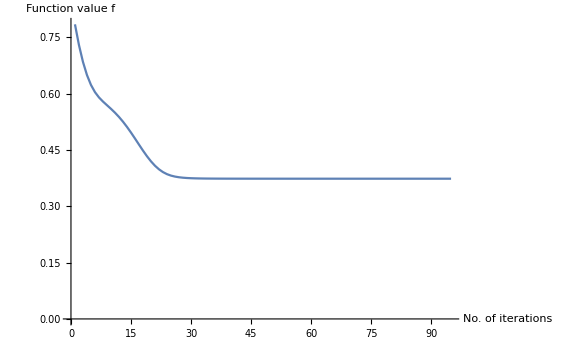

```mathematica
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

## Bosonic Complexity of Purification (CoP)

```mathematica
mass=.1;
latticespacing=1.;
sites=100;
dimA1=1;
dimB1=3;
sep=50;
dimPur=dimA1+dimB1;
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for a lattice free scalar field theory

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In the example below, the mixed state is obtained for a system with total number of lattice sites 100 with 3 sites per subsystem in the initial system, mass term 0.1, lattice spacing 1, 
and no lattice sites separating the subsystems.

```mathematica
CM0=partialCM[100,mass,latticespacing,sep,dimA1,dimB1]; CM0//MatrixForm
```

(1.28101 | 0 | -5.21181×10^-6 | 0 | -5.35149×10^-6 | 0 | -5.58759×10^-6 | 0
0 | 1.39418 | 0 | 0.00236743 | 0 | 0.00241066 | 0 | 0.00248335
-5.21181×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00236743 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-5.35149×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00241066 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-5.58759×10^-6 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00248335 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];

M0=ArrayFlatten[{{Inverse[MTra],0},{0, Inverse[MTra]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,0.1},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricSp[LieBasis,JR0]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,JR0,+1];


SystemSpecific={JR0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 3.26563 seconds

Final value: 0.984995

Number of iterations: 6

Number of total corrections: 0

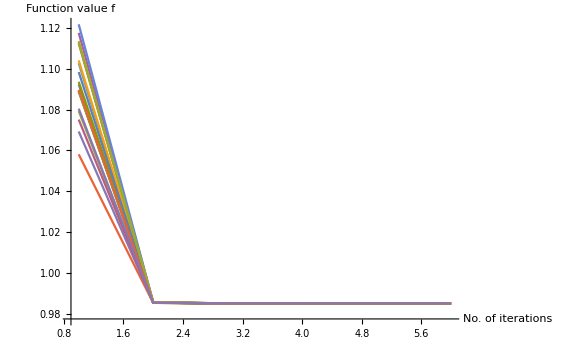

```mathematica
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

## Fermionic Entanglement of Purification (EoP)

```mathematica
NN=10; (* Total number lattice sites *)
J=2;h=2;γ=-1; (* XY model parameter*)
dimA1=1; dimB1=1; (* dofs of chosen subystems *)
d=1; (* distance subsystems *)
dimA2=dimA1;dimB2= dimB1;(* purifying dofs, dimA2+dimB2 ≥ dimA1+dimB1 *)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

```mathematica
Egroundstate=-1/2 Sum[ϵ[(2π k)/NN+π/NN],{k,1,NN}]//N
```

-12.7849

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[(2π k+π)/NN]]^2-Abs[u[(2π k+π)/NN]]^2//N)Cos[(2π k+π)/NN(j-l)]+2Im[v[(2π k+π)/NN]u[(2π k+π)/NN]]Sin[(2π k+π)/NN(j-l)],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Ω0=JJ[[indices,indices]]; Ω0//MatrixForm
```

(0 | 0.639245 | 0 | -0.220269
-0.639245 | 0 | -0.141421 | 0
0 | 0.141421 | 0 | 0.639245
0.220269 | 0 | -0.639245 | 0)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
J0=GOPurifyStandardJFermion[rlist,dimA2+dimB2,"qpqp"];
MTra//Dimensions
```

{4,4}

#### 4. Define the problem-specific input arguments

```mathematica
Restriction=GORestrictionAA[{dimA1,dimB1,dimA2,dimB2}];
function=GOEoPFerm[Restriction]; gradient=GOEoPgradFerm[Restriction];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimA2+dimB2]}];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimA2+2dimB2]}}]//SparseArray;
M0List=Table[M0.MatrixExp[RandomReal[{0,0.1},Length[LieBasis]].LieBasis],{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricO[LieBasis]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,J0,-1];

SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 0.774057 seconds

Final value: 0.0697032

Number of iterations: 43

Number of total corrections: 0

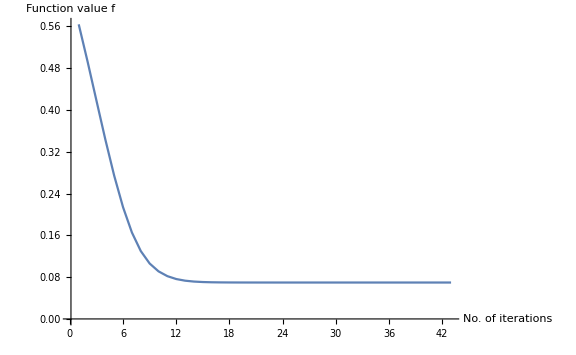

```mathematica
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
finM=Result⟦2,1⟧;
finM.Transpose[finM]//Eigenvalues
finJ=finM.J0.Transpose[finM];
finJ.finJ//Eigenvalues
function[finM,J0]
```

{1.,1.,1.,1.,1.,1.,1.,1.}

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

0.0697032

```mathematica
EE[Ω0⟦1;;4,1;;4⟧]
EE[Ω0⟦1;;2,1;;2⟧]
```

0.90208

0.471965

## Fermionic Complexity of Purification (CoP)

```mathematica
NN=10; (* Total number lattice sites *)
J=2;h=2;γ=-1; (* XY model parameter*)
dimA1=1; dimB1=1; (* dofs of chosen subystems *)
d=1; (* distance subsystems *)
dimPur=dimA1+dimB1;(* purifying dofs, dimPur ≥ dimA1+dimB1 *)
JR0=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state *)
```

#### 0. Initialize definitions: Functions to generate the initial covariance matrices for the XY model

```mathematica
ϵ[k_]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]=-J Cos[k]-h;
b[k_]=γ J Sin[k];
u[k_]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
```

```mathematica
Egroundstate=-1/2 Sum[ϵ[(2π k)/NN+π/NN],{k,1,NN}]//N
```

-12.7849

#### 1. Generate the initial mixed state covariance matrix

Note: The functions used to define the initial mixed state covariance matrix below are beyond the scope of the GaussianOptimization.m package and are not included in it.
In this case we are generating a covariance matrix for a system with a total of 10 lattice sites and partitioning it into two adjacent subsystems containing 2 lattice sites each.

```mathematica
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0;
Ωblock=1/NN Table[Sum[(Abs[v[(2π k+π)/NN]]^2-Abs[u[(2π k+π)/NN]]^2//N)Cos[(2π k+π)/NN(j-l)]+2Im[v[(2π k+π)/NN]u[(2π k+π)/NN]]Sin[(2π k+π)/NN(j-l)],{k,0,NN-1}],{j,1,NN},{l,1,NN}];
ΩΩ=ArrayFlatten[({{0, Ωblock}, {-Transpose[Ωblock], 0}})];JJ=ΩΩ;
```

```mathematica
dim1=dimA1;dim2=dimB1;dim=NN;
indices1=Thread[{Table[x,{x,dim1}],Table[x+dim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+dim,{x,dim2}]}]//Flatten[#,1]&;
indices=Join[indices1,indices2];

Ω0=JJ[[indices,indices]]; Ω0//MatrixForm
```

(0 | 0.639245 | 0 | -0.220269
-0.639245 | 0 | -0.141421 | 0
0 | 0.141421 | 0 | 0.639245
0.220269 | 0 | -0.639245 | 0)

#### 2. Generate the purified state complex structure (in this case for a minimal purification)

```mathematica
{rlist,MTra}=GOExtractStdFormΩ[Ω0];
JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
```

#### 4. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

#### 5. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSO[dimPur]}];
M0=ArrayFlatten[{{Inverse[MTra],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray;
M0List=Table[MatrixExp[RandomReal[{0,.1},Length[LieBasis]].LieBasis].M0,{i,50}];

newM[m_,s_,x_]:=m.GOapproxExp[s,x];

metric=GOMetricO[LieBasis]; (*not needed, from older version for comparison) *)
geometry=GOGeometryConst[LieBasis,JR0,-1];

SystemSpecific={JR0,M0List,LieBasis,geometry,newM};
```

#### 6. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=True; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### 7. Run the Optimization

```mathematica
{time,Result}=AbsoluteTiming[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

#### 8. Evaluate the result

Time taken: 0.510357 seconds

Final value: 0.610713

Number of iterations: 5

Number of total corrections: 0

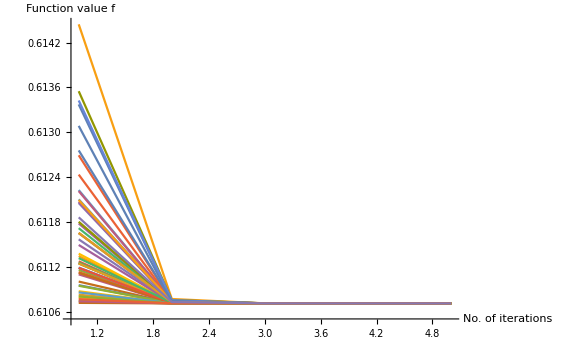

```mathematica
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
(* We plot all items in the finalElist object in the result to ensure a correct plot in the case of multiple results *)
```

```mathematica
finM=Result⟦2,1⟧;
finM.Transpose[finM]//Eigenvalues
```

{1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
EE[J_]:=-1/2 Sum[(1+x)/2 GOlogfunction[(1+x)/2]+(1-x)/2 GOlogfunction[(1-x)/2],{x,Im[Eigenvalues[J]]}]
```

```mathematica
EE[JJ⟦1;;4,1;;4⟧]
EE[JJ⟦1;;2,1;;2⟧]
```

2 Log[2]

Log[2]

# Setting up a custom optimization

This section is intended as a concise guide to applying the GaussianOptimization.m package and its functions to an arbitrary optimization problem.
As shown in the function description for GOOptimize above, the input arguments for the optimization can be grouped into three categories:

#### 1. Problem-Specific input arguments

These are the arguments that are related specifically to the physical quantity under investigation. They are:

f -- The function to be optimized (must be a function of the transformation M, and the initial state complex structure J_0)

df -- The gradient associated with the function to be optimized (must be a function of the transformation M, the initial state complex structure J_0, the Lie algebra basis K, and the inverse metric G^-1)

#### 2. System-Specific input arguments

These are the arguments that are related to the geometry of the manifold over which the optimization is conducted, including also the points in the manifold, from which the optimization is initialized. Changing the system-specific arguments while keeping all other arguments the same means changing only the landscape on which the gradient descent is performed.
Import note: All system specific input arguments must be in the basis (q_1,p_1,q_2,p_2,...)!

J_0 -- The initial state complex structure

{M_0} -- A list of the initial transformations to be applied to J_0 (together with J_0, these transformations parametrize the starting points for the gradient descent)

{K_i} -- The Lie algebra basis

G^-1 -- The inverse natural metric

These input arguments are key to the theory underlying this optimization algorithm: The inverse natural metric is used by the gradient function to calculate a consistent value for the gradient vector, independent of basis choice. More importantly, it should be noted that any constraints on the optimization are implemented by restricting the Lie algebra basis to those elements K_i which generate transformations that only transform within the restricted class of states of interest.

#### 3. Procedure-Specific input arguments

These input arguments specify parameters relating to the numerical implementation of the optimization. Firstly, this includes three stopping criteria:

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

tol_F -- Tolerance on the function values (stopping criterion: (F_(n+1)-F_n)/F_(n+1)<tol_F)

lim_iter  -- Limit on the number of iterations (stopping criterion: n>lim_iter; the default value of this argument is ∞)

The algorithm is terminated as soon as any of the three stopping criteria is violated by all of the trajectories still under consideration.

Secondly, the procedure-specific input arguments include the sub-routine for correcting the step size in the case where F_(n+1)>F_ninitially. This subroutine must be of function of the current step size only, which returns only the new step size. The most rudimentary implementation, used in the examples above, is simply step(ϵ)=ϵ/2.

Thirdly, the input arguments include optional arguments for debugging modes of the algorithm. In particular, at the moment there is only one such optional parameter, which tales either True or False as values, where False corresponds to running the algorithm in its most efficient version, without debugging.

track all trajectories? -- This completes the full optimization procedure for all starting points, rather than only the most promising trajectories